# Lotka Oscillations

## Undamped oscillations from a basic set of mass action equations

Alfred Lotka
"Undamped Oscillations from the Law of Mass Action"
Journal of the American Chemical Society 49:1595-1599 (1920)

```mathematica
<<xlr8r.m
```

xlr8r 0.74 (13 May 2009) loaded 25 October 2009 at 10:47 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

### Here is the simple Lotka Reaction Set

Basic Scheme:
	X        -> X + X
	X + Y -> Y + Y
	Y        -> ∅

```mathematica
net={{X-> 2X, k1}, {X+Y-> 2Y, k2}, {Y-> ∅, k3}}
```

{{X→2 X,k1},{X+Y→2 Y,k2},{Y→∅,k3}}

#### look at the steady states

```mathematica
interpret[net][[1]]//TableForm
```

X'[t]==k1 X[t]-k2 X[t] Y[t]
Y'[t]==-k3 Y[t]+k2 X[t] Y[t]

```mathematica
ss=steadyState[net]
```

{{X[t]→0,Y[t]→0},{X[t]→k3/k2,Y[t]→k1/k2}}

```mathematica
J=jacobianMatrix[net]
```

{{k1-k2 Y[t],-k2 X[t]},{k2 Y[t],-k3+k2 X[t]}}

```mathematica
Eigenvalues[J]/.ss/.{k1-> 1, k2-> 2, k3-> 1}
```

{{-1,1},{-ⅈ,ⅈ}}

#### run the simulation

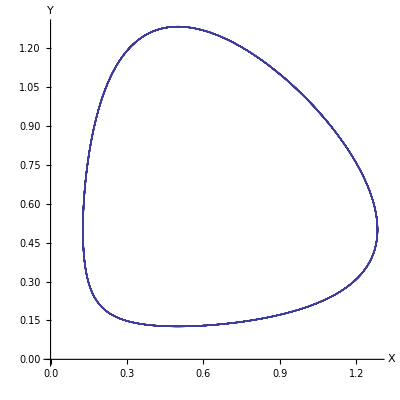

```mathematica
n=run[net,  rates-> {k1-> 1, k2-> 2, k3-> 1}, initialConditions-> { X-> 1.1, Y-> .9}, timeSpan-> 50];
PhasePlot[n, {X,Y}, {0, 50}, AspectRatio-> 1]
```

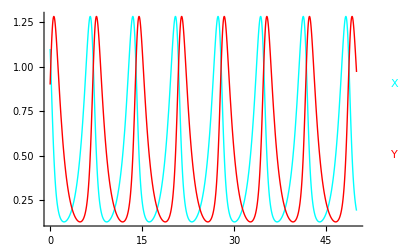

```mathematica
runPlot[n]
```

### Do a Stream Plot

```mathematica
Last/@(interpret[net][[1]])/.{X[t]-> X, Y[t]-> Y}
```

{k1 X-k2 X Y,-k3 Y+k2 X Y}

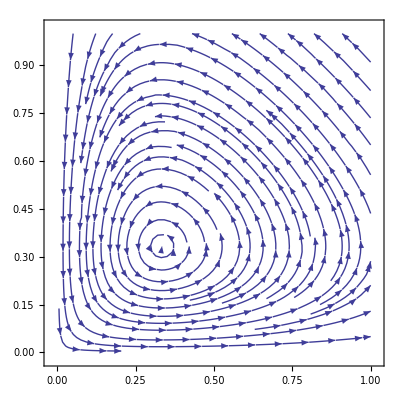

```mathematica
StreamPlot[{k1 X-k2 X Y,-k3 Y+k2 X Y}/.{ k1-> 1, k2-> 3, k3-> 1}, {X, 0, 1}, {Y, 0, 1}]
```

### Save a CelleratorML file

```mathematica
<<CelleratorML.m
```

Cellzilla2D (2.1.α.18 5 Sept 2009) loaded Sun 25 Oct 2009 10:51:15 using xlr8r 0.74 (13 May 2009) and xSSA 1.1.α.5 (23-Jul-2009)

CelleratorML 1.0.5 (19 June 2009) loaded 25 October 2009 at 10:51 GMT-06:60 using Mathematica Version 7.0 for Linux x86 (64-bit) (February 18, 2009) Release 1

```mathematica
SaveModel["Lotka-MassAction-Oscillations.xml", net,  "InitialConditions"-> {X-> 1.1, Y-> .9},
"Parameters"-> {k1-> 1, k2-> 1, k3-> 1}, 
"Model"-> "Lotka-Oscillations"]
```

Lotka-MassAction-Oscillations.xml

Model: Model4

CelleratorML Version: 1.0

3 reactions

3 parameters

2 initial values

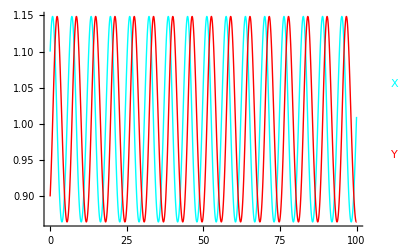

```mathematica
{model, parms, iv, opts}=GetModel["Lotka-MassAction-Oscillations.xml"];
run[model, initialConditions-> iv, rates-> parms];
runPlot[%]
```